```mathematica
ClearAll["Global`*"]
```

```mathematica
L=1;
h=1;
R=0.2;
c={L/2,h/2};
```

```mathematica
ra[t_]:={c[[1]]+R Cos[2π t],c[[2]]+R Sin[2π t]}
rb[t_]:=ra[t]+u[ra[t]]
```

```mathematica
u[r_]:={0.1 r[[1]], 0.5 r[[2]]r[[1]]}
```

```mathematica
ua[x_]:=x^2
```

```mathematica
sa[t_]:=NIntegrate[Norm[ra'[s]],{s,0,t}]
sb[t_]:=NIntegrate[Norm[rb'[s]],{s,0,t}]
```

```mathematica
(*read u_a*)
ta=Import["/Users/michelecastellana/Documents/finite_elements/fluid_structure_interaction/fluid_obstacle/remesh/solution/u_a_test.csv"]
ta=Table[{ta[[i,2]],ta[[i,1]]},{i,2,Length[ta]}]
```

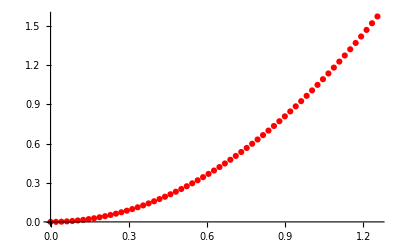

```mathematica
plotuanum=ListPlot[ta,PlotStyle->Red]
```

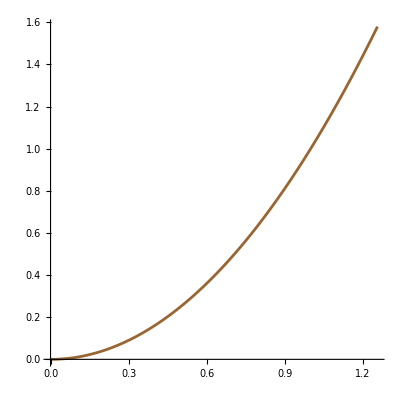

```mathematica
plotuaex=ParametricPlot[{sa[t],ua[sa[t]]},{t,0,1},PlotStyle->Brown,AspectRatio->1]
```

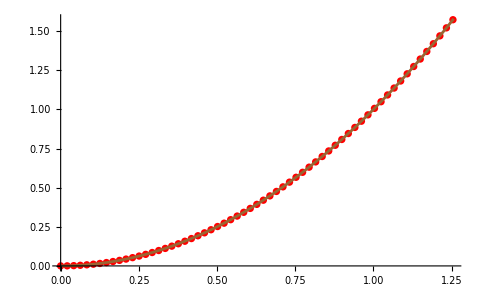

```mathematica
Show[plotuanum,plotuaex]
```

```mathematica
(*read u_b*)
```

```mathematica
tb=Import["/Users/michelecastellana/Documents/finite_elements/fluid_structure_interaction/fluid_obstacle/remesh/solution/u_b_test.csv"]
tb=Table[{tb[[i,2]],tb[[i,1]]},{i,2,Length[tb]}]
```

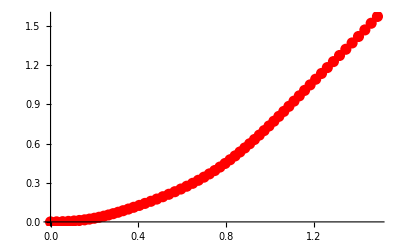

```mathematica
plotubnum=ListPlot[tb,PlotStyle->{Red,PointSize->.02}]
```

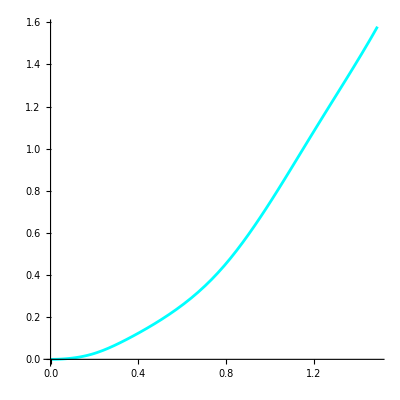

```mathematica
plotubex=ParametricPlot[{sb[t],ua[sa[t]]},{t,0,1},PlotStyle->Cyan,AspectRatio->1]
```

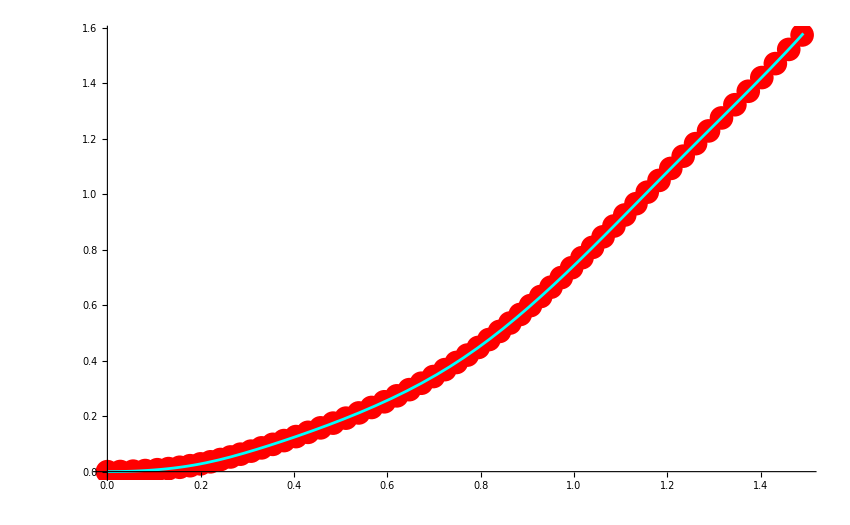

```mathematica
Show[plotubnum,plotubex]
```